```mathematica
FileNameForVotes[ primes_] := Module[{fileName, temp, sep, p, pPos},
sep = "\\";
temp ="d:\\triangle\DataSrc";
For[pPos =1, pPos <= Length[primes], pPos++,
temp = StringJoin[temp, sep, ToString[primes[[pPos]]]];
];
temp = StringJoin[temp, "\\Solutions.txt"];
fileName = temp;
Return[fileName]
]
```

```mathematica
FileNameForVotes[{7,11,13,19}]
```

d:\triangle\DataSrc\7\11\13\19\Solutions.txt

```mathematica
data=ReadList[FileNameForVotes[{7,11,13,19}],Number]
```

{«1»}

```mathematica
Length[data]
```

7546

```mathematica
Table[IntegerPart[Log[10,d+1]], {d,data}]
```

{0,0,0,0,1,1,2,2,2,2,2,2,3,4,4,4,16,16,16,16,16,16,44,44,44,44,44,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,120,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,138,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,141,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,147,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,167,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,173,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,225,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,240,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,297,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,320,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,423,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,481,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,950,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,1414,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200,2200}

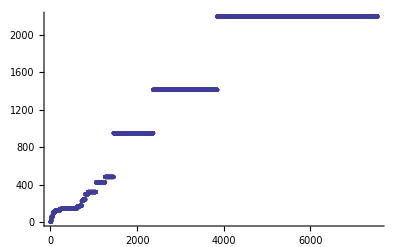

```mathematica
ListPlot[Table[IntegerPart[Log[10,d+1]], {d,data}]]
```

```mathematica
Tally[ Table[IntegerPart[Log[d+1]], {d,data}]]
```

{{0,2},{1,2},{4,2},{5,4},{6,2},{7,1},{10,3},{37,6},{101,5},{132,28},{231,33},{240,21},{278,105},{319,45},{326,324},{338,39},{386,60},{398,40},{518,37},{554,44},{686,61},{737,185},{976,210},{1109,198},{2189,913},{3256,1478},{5066,3698}}

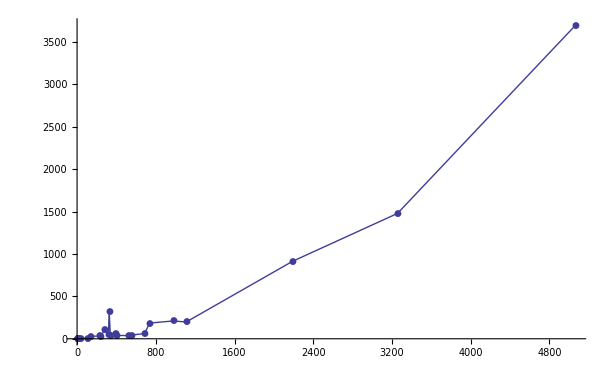

```mathematica
ListPlot[Tally[ Table[IntegerPart[Log[d+1]], {d,data}]], Joined->True, PlotRange->All, PlotMarkers->Automatic]
```

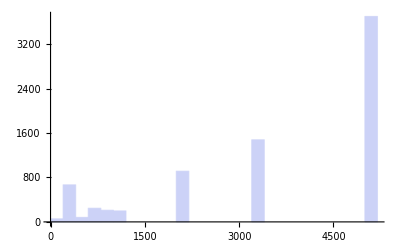

```mathematica
Histogram[Table[IntegerPart[Log[d+1]], {d,data}],  PlotRange->All]
```

```mathematica
Tally[ Table[IntegerPart[Log[7*11*13*19,d+1]], {d,data}]]
```

{{0,13},{1,3},{3,6},{10,5},{13,28},{23,33},{24,21},{28,105},{32,45},{33,324},{34,39},{39,60},{40,40},{52,37},{56,44},{69,61},{74,185},{99,210},{112,198},{222,913},{330,1478},{514,3698}}

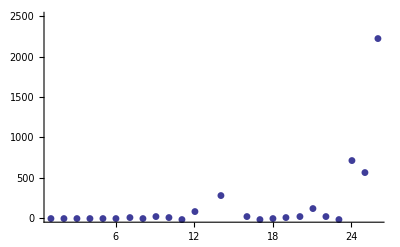

```mathematica
ListPlot[Differences[ Map[#[[2]]&,Tally[ Table[IntegerPart[Log[d+1]], {d,data}]]]],  PlotRange->{All,{0,2500}}, PlotMarkers->Automatic]
```

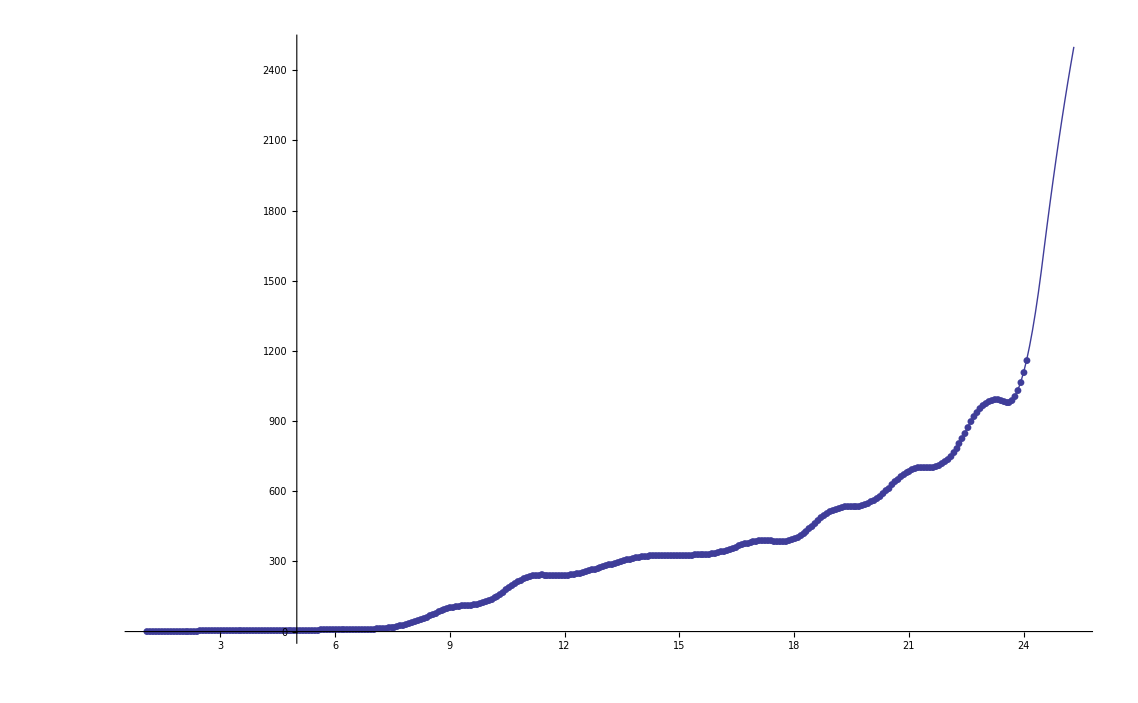

```mathematica
ListPlot[ Map[#[[1]]&,Tally[ Table[IntegerPart[Log[d+1]], {d,data}]]],  PlotRange->{All,{0,2500}}, PlotMarkers->Automatic, InterpolationOrder->2, Joined->True]
```

```mathematica
Map[#[[1]]&,Tally[ Table[IntegerPart[Log[d+1]], {d,data}]]]
```

{0,1,4,5,6,7,10,37,101,132,231,240,278,319,326,338,386,398,518,554,686,737,976,1109,2189,3256,5066}

```mathematica
FindFit[Map[#[[1]]&,Tally[ Table[IntegerPart[Log[d+1]], {d,data}]]], c x + d x ^2, {c,d}, x]
```

{c→-95.9673,d→7.57292}

```mathematica
FindFit[Map[#[[1]]&,Tally[ Table[IntegerPart[Log[d+1]], {d,data}]]], a ^(b x), {a,b}, x]
```

{a→1.14847,b→2.25412}

```mathematica
With [{a=1.1484665606103663,b=2.25411506404466},
Plot[a ^(b x), {x,0,100}]]
```

```mathematica
est[x_]:=1.1484665606103663 ^( 2.25411506404466 x )
```

```mathematica
est[29]
```

8509.36

```mathematica
N[E^8509.361426741583]
```

3.70435119956×10^3695

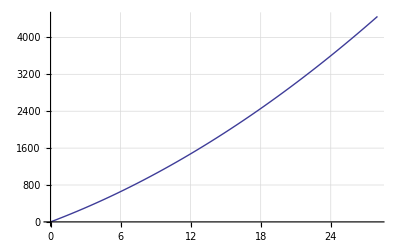

```mathematica
With [{a=1.1484665606103663,b=2.25411506404466},
Plot[95.96732055056528 x + 2.25411506404466 x^2, {x,0,28}, GridLines->Automatic]]
```

```mathematica
FullSimplify[Fit[Tally[ Table[IntegerPart[Log[d+1]], {d,data}]],{1,x,x^2, x^3},  x]]
```

6.60867×10^-9 (44.5263+x) (1813.64+x) (10807.6+x)

```mathematica
FindFit[Map[#[[1]]&,Tally[ Table[IntegerPart[Log[d+1]], {d,data}]]], a ^(b x), {a,b}, x]
```

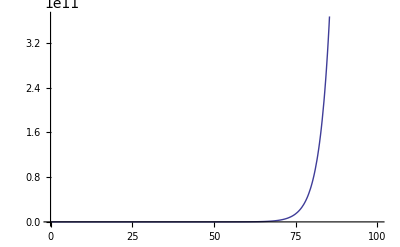

```mathematica
With [{a=1.1484665606103663,b=2.25411506404466},
Plot[a ^(b x), {x,0,100}]]
```